{{0,0.15},{1,0.55},{2,1.25},{3,2.15},{4,3.35},{5,4.85},{6,6.65},{7,8.65},{8,10.95},{9,13.55},{10,16.35},{11,19.45}}

{{0,0.137078},{1,0.137078},{2,1.2337},{3,2.19325},{4,3.42695},{5,4.9348},{6,6.71681},{7,8.77298},{8,11.1033},{9,13.7078},{10,16.5864},{11,19.7392}}

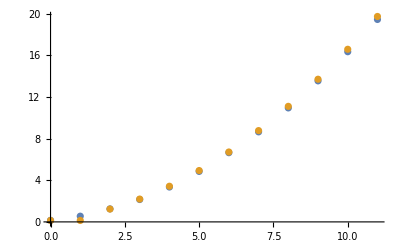

```mathematica
A={{0,0.15000000000000002},{1,0.55},{2,1.25},{3,2.1500000000000004},{4,3.3500000000000014},{5,4.849999999999999},{6,6.649999999999992},{7,8.649999999999984},{8,10.949999999999978},{9,13.549999999999969},{10,16.349999999999962},{11,19.450000000000006}}
B={{0,0.137077838904},{1,0.137077838904},{2,1.23370055014},{3,2.1932454224},{4,3.4269459726},{5,4.9348022005},{6,6.7168141063},{7,8.77298168986},{8,11.1033049512},{9,13.7077838904},{10,16.5864185074},{11,19.7392088022
}}
ListPlot[{A,B}]
```

Exact Solution settings( a=6)
A is computer generated. B is the exact solution. 
potential=lambda E:RungeKutta(-4,0,.01,.01,4,lambda t,y,z:z,lambda t,y,z:(y*2*(E-V(t,p)))/c)[2][-1]

def V(x,p): #Infiite Square Wall
    if x>-3 and x<3:
        return 0
    else :
        return 10**3